# Report Project 2 Signal Processing

Course code: II1303
Date: 2021-12-

Natasha Donner, ndonner@kth.se
Magnus Tomsic, mtomsic@kth.se
Mohamad Abou Helal, mohamaah@kth.se

## Summery

### Part 1

Consider the system function of an IIR filter

H(z) = ((1 - z^-1)∏_(k=1)^4 (1 - z^-1 e^(-j 0.11π (2k-1)))(1 - z^-1 e^(j 0.11π (2k-1))))/(100 ∏_(k=1)^4 (1 - 0.9 z^-1 e^(-j 0.22π k))(1 - 0.9 z^-1 e^(j 0.22π k)))

a) Make a pole-zero plot of H(z). Is the system stable?

A system is stable if the poles of H(z)lie strictly inside the unit circle. 

X = poles
O = zeros 

As we can see in the plot all poles lies inside the unit circle, which makes the system stable.

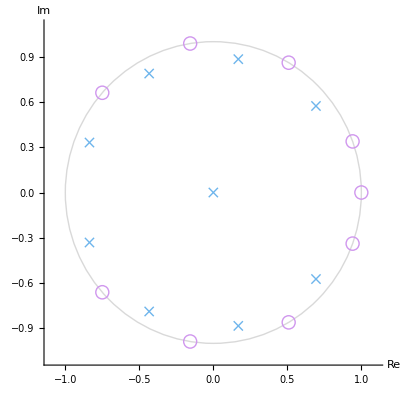

b) Discuss how the filter works, what happens with certain frequencies?

The filter works as a high pass filter and blocks low frequency.

c) Illustrate the frequency response of the IIR filter!

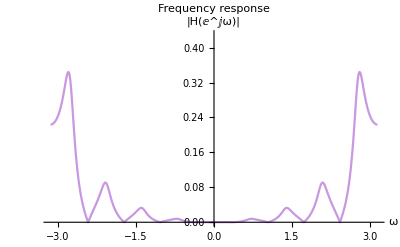

d) Sketch a direct form structure to illustrate the IIR filter!

e) Consider the continuous signal x(t) defined as

x(t) = 1/π∑_(k=1)^9 (-1 )^(k-1)/k sin(2π f_0 k t)

with f_0=220 Hz. This signal is sampled with the frequency f_s=4 kHz. Plot the sampled signal x[n]!

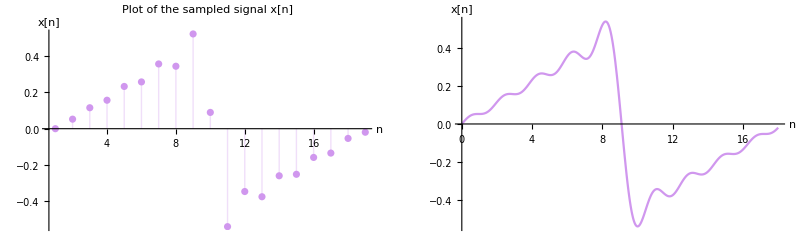

f) Now, the sampled signal x[n] is input to the IIR filter above. Compute and plot the output signal y[n]!

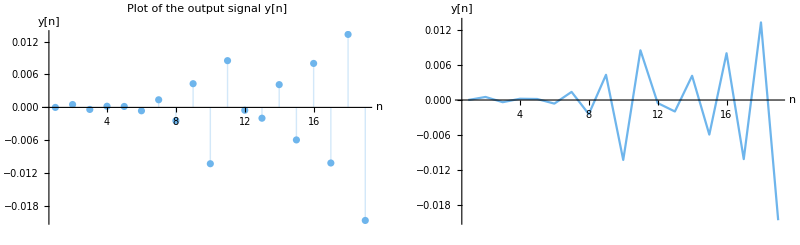

g) Draw and compare the two-sided spectrum of x[n] and that of y[n]!

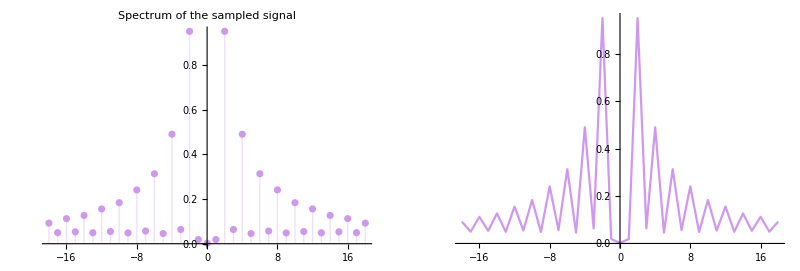
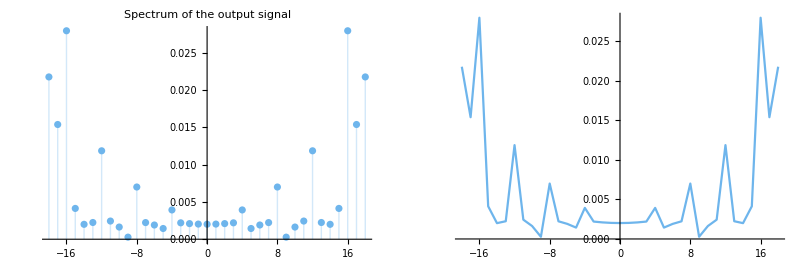

### Part 2

Consider the following signal

x(t) = [ⅇ^(-50t)cos(2π100 t)+ⅇ^(-75t)cos(2π200 t)+ⅇ^(-100t)cos(2π300 t)]u(t)

a) Make a plot of x(t) as function of time!

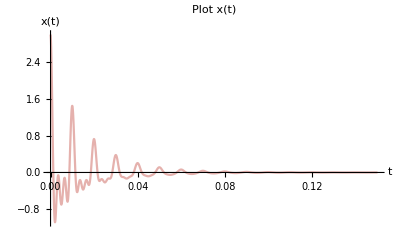

b) Compute the spectrum X(jω)!

```mathematica
((-50+ⅈ ω)/(-40000 π^2+(50 ⅈ+ω)^2)+(-75+ⅈ ω)/(-160000 π^2+(75 ⅈ+ω)^2)+(-100+ⅈ ω)/(-360000 π^2+(100 ⅈ+ω)^2))/(√(2 π))
```

c) Plot |X(jω)| and arg (X(jω))!

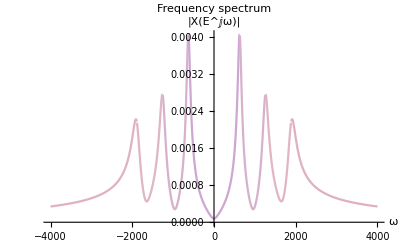

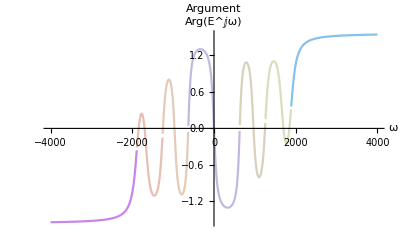

d) There are some distinct local maxima and minima in the spectrum. Solve for these frequencies!

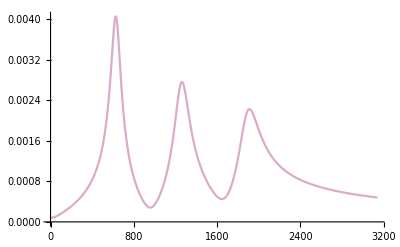

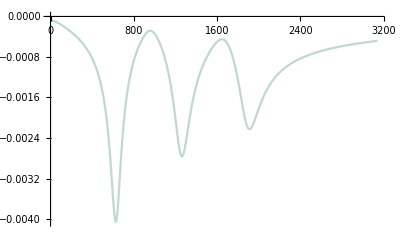

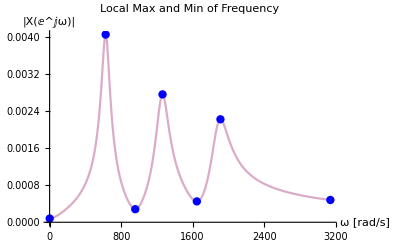

e) Can you motivate the local maxima from the expression of x(t)?

The local maxima can be find from the expression of x(t). The omega values will be the max x coordinate. From the expression we obtain 3 omega values: 2π100, 2π200, 2π300. This correspond to the x values we get from the FindPeaks function. {(627,0.00405668),(1263,0.00276316),(1911,0.00222517)}

## Code

```mathematica
ClearAll["Global`*"]
```

### Package II1303

The following package introduces the methods

Reconstruct, Afϕ, Aωϕ,
ToExp, Poles, Zeros, PoleZeroPlot, 
ZTransform2, InverseZTransform2, ZApart, 
LaplaceTransform2, InverseLaplaceTransform2

#### Code

```mathematica
(* Ver. 151125, goeran@kth.se *)
BeginPackage["II1303`"]; 
Unprotect[{ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 
Reconstruct::usage = "Reconstruct[fs][{f,A,ϕ}] returns the shifted or folded  \
{f,A,ϕ} list due to sampling. Reconstruct[ωs][{ω,A,ϕ}] is also valid.";
fAϕ::usage = "fAϕ[t][Cos|Sin|Exp[arg]] extracts {f,A,ϕ} information.";
ωAϕ::usage = "ωAϕ[t][Cos|Sin|Exp[arg]] extracts {ω,A,ϕ} information.";
ToExp::usage = "ToExp[z] = Abs[z]*E^(I*Arg[z]) returns a complex number in \
exponential form.\nFor floating point complex numbers use ReleaseHold in orer to \
evaluate."; 
TrigCombine::usage = "ToExp[a*trig[x+α] + b*trig[x+β]], where trig is Cos or Sin, \
returns A*trig[x+v].";
Poles::usage = "Poles[H, z] returns the poles of the system function H[z]."; 
Zeros::usage = "Zeros[H, z] returns the zeros of the system function H[z]."; 
PoleZeroPlot::usage = "PoleZeroPlot[H, z] plots poles and zeros of the system \
function H[z].\nPoleZeroPlot takes the same options as ListPlot."; 
PoleMarker::usage = "PoleMarker is an option for PoleZeroPlot that defines the \
graphics for the pole marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...]."; 
ZeroMarker::usage = "ZeroMarker is an option for PoleZeroPlot that defines the \
graphics for the zero marker.\nIt is assumed to be a Function[{postition, \
multiplicity, scale}, ...].";
MarkerScale::usage = "MarkerScale is an option for PoleZeroPlot that defines the \
scale for the pole and zero marker."; 
ZTransform2::usage = "ZTransform2[x, n, z] returns the bilateral, 1D z-transform.\n\
It evaluates FourierSequenceTransform[x,n,-I Log[z]]."; 
InverseZTransform2::usage = "InverseZTransform2[X, z, n] returns the bilateral, 1D \
inverse z-transform.\nIt evaluates InverseFourierSequenceTransform[X /. z -> \
E^(I*ω), ω, n]."; 
FactorAll::usage = "FactorAll[p, x] returns a product of first degree factors."; 
ZApart::usage = "ZApart[X, z] = Expand[z*Apart[X/z,z]] returns an expression \
suitable for inverse z-transform."; 
LaplaceTransform2::usage = "LaplaceTransform2[x, t, s] returns the bilateral, 1D \
Laplace transform.\nIt evaluates FourierTransform[x, t, -I*s]."; 
InverseLaplaceTransform2::usage = "InverseLaplaceTransform2[X, s, t] returns the \
bilateral, 1D inverse Laplace transform.\nIt evaluates InverseFourierTransform[X /. \
s -> I*ω, ω, t].";
 
Begin["`Private`"];
Reconstruct[(fs_)?Positive][{f_,A_,ϕ_}]:=
Module[
	{fa,ϕa=ϕ},
	(* shift *)
	fa=Mod[Abs[f], fs];
	(* fold *)
	If[fa>fs/2,fa=fs-fa;ϕa=-ϕ];
	If[fa>0,{Sign[f]*fa,A,ϕa},{0,A,ϕa}]
];

Reconstruct[fs_][data:{{_, _, _}..}] := 
Module[{data1,data2,data3}, 
	data1 = Reconstruct[fs] /@ data;
	data2 = Gather[data1, #1[[1]] == #2[[1]] & ];
	({#1[[1,1]], Norm[#1[[All,2]] . E^(I*#1[[All,3]])], Arg[#1[[All,2]] . E^(I*#1[[All,3]])]} & ) /@ data2
];

fAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]+Arg[A]};
fAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t]/(2π),Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
fAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/(2π ⅈ),Abs[A],Coefficient[z,t,0]/ⅈ+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Cos[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Sin[x_]]:={Coefficient[x,t],Abs[A],Coefficient[x,t,0]-π/2+Arg[A]};
ωAϕ[t_Symbol][(A_:1)Exp[z_]]:={Coefficient[z,t]/ⅈ,Abs[A],Coefficient[x,t,0]/ⅈ+Arg[A]};
 
ToExp[z:Complex[_Real, _Real]] := Abs[z]*HoldForm[E]^(I*Arg[z]); 
ToExp[(z_)?NumericQ] := Abs[z]*E^(I*Arg[z]); 
ToExp[z___] := z; 
SetAttributes[ToExp, Listable];

TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Cos[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) + b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Cos[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) - I*b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
TrigCombine[(a_:1)*Sin[(x_) + (u_:0)] + (b_:1)*Sin[(x_) + (v_:0)]] := 
  Simplify[ComplexExpand[Abs[a*E^(I*u) + b*E^(I*v)]]*
   Cos[x + ComplexExpand[Arg[(-I)*a*E^(I*u) - I*b*E^(I*v)]]], ExcludedForms -> {_Sin, _Cos}];
SetAttributes[TrigCombine, HoldAll];

Poles[H_, z_Symbol] := Flatten[
	TransferFunctionPoles[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Poles[H:_Symbol | _Function, z_Symbol] := Poles[H[z], z];
 
Zeros[H_, z_Symbol] := Flatten[
TransferFunctionZeros[TransferFunctionCancel[TransferFunctionModel[H, z]]]
]; 
Zeros[H:_Symbol | _Function, z_Symbol] := Zeros[H[z], z];
 
Options[PoleZeroPlot] = Join[{
	PoleMarker :> ({
		ColorData["Pastel"][1], Thickness[Large],
		Line[{#1 + #3*{-1, -1}/√2, #1 + #3*{1, 1}/√2}], 
		Line[{#1 + #3*{-1, 1}/√2, #1 + #3*{1, -1}/√2}], 
		If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ), 
	ZeroMarker :> ({
		ColorData["Pastel"][0.1], Thickness[Large],
		Circle[#1, #3], 
        If[#2 > 1, Text[#2, #1 + #3*{√2, √2}, {-1, 0}], Sequence @@ {}]} & ),
	MarkerScale -> Automatic
	}, 
	Options[Graphics]
]; 
SetOptions[PoleZeroPlot, AspectRatio -> Automatic, Axes -> True, PlotRange -> Automatic]; 
PoleZeroPlot[H_, z_Symbol, opts:OptionsPattern[]] := Module[
	{xy, x, y, d, pp, pz, mp, mz, s, r, 𝕡, 𝕫, range, allopts, s0=Scaled[0.015]}, 
	xy := {Re[#1], Im[#1]} & ; 𝕡 = Poles[N[H], z]; 𝕫 = Zeros[N[H], z]; 
	pp = xy /@ DeleteDuplicates[𝕡]; pz = xy /@ DeleteDuplicates[𝕫]; 
	mp = Length /@ Gather[𝕡]; mz = Length /@ Gather[𝕫]; 
	x = Join[pz[[All,1]], pp[[All,1]]]; y = Join[pz[[All,2]], pp[[All,2]]]; 
	If[OptionValue[PlotRange] === Automatic, 
		x = Join[{-1, 1}, x]; y = Join[{-1, 1}, y]
	]; 
	range = ({Min[#1], Max[#1]} & ) /@ {x, y}; 
	d = 0.05*Apply[Subtract, range, {1}]; range = range + Transpose[{d, -d}]; 
	allopts = FilterRules[Join[{opts}, Options[PoleZeroPlot]], Options[Graphics]]; 
	If[OptionValue[PlotRange] === Automatic || OptionValue[PlotRange] === All, 
		PrependTo[allopts, PlotRange -> range]
	]; 
	s = OptionValue[MarkerScale];
	If[ s=== Automatic, s = s0];
	If[ ! MatchQ[s, _?NumericQ] && ! MatchQ[s, Scaled[_?NumericQ]], s = s0];
	If[MatchQ[s, Scaled[_?NumericQ]],
		s = First[s];
		r = PlotRange/.AbsoluteOptions[Graphics[Point[Join[pp,pz]],Sequence @@ allopts],PlotRange];
		If[MatchQ[r,{{_?NumberQ,_?NumberQ},{_?NumberQ,_?NumberQ}}],s*=Min[-Subtract@@@r]]
	];
	Graphics[{
		Apply[OptionValue[PoleMarker], (Join[#1, {s}] & ) /@ Transpose[{pp, mp}], {1}], 
		Apply[OptionValue[ZeroMarker], (Join[#1, {s}] & ) /@ Transpose[{pz, mz}], {1}]
		}, Sequence @@ allopts
	]
];
PoleZeroPlot[H:_Symbol | _Function, z_Symbol, opts:OptionsPattern[]] := PoleZeroPlot[H[z], z, opts]; 

Options[ZTransform2] = Rest[Options[FourierSequenceTransform]]; 
ZTransform2[x_, n_Symbol, z_, opts:OptionsPattern[]] := 
	FourierSequenceTransform[x, n, (-I)*Log[z], FourierParameters -> {1, 1}, opts];
ZTransform2[x:_Symbol | _Function, n_Symbol, z_, opts:OptionsPattern[]] := 
	ZTransform2[x[n], n, z, opts]; 

Options[InverseZTransform2] = Rest[Options[InverseFourierSequenceTransform]]; 
InverseZTransform2[X_, z_Symbol, n_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierSequenceTransform[X /. z -> E^(I*ω), ω, n, FourierParameters -> {1, 1}, opts]
]; 
InverseZTransform2[X:_Symbol | _Function, z_Symbol, n_, opts:OptionsPattern[]] := 
	InverseZTransform2[X[z], z, n, opts];

FactorAll[p_, x_Symbol] := Module[
{a, z, q}
, a = Coefficient[p, x, Exponent[p, x]]; 
q = p/a; z = x /. Solve[q == 0, x, Complexes]; 
Times @@ Join[{a}, x - z]
] /; PolynomialQ[p, x];

ZApart[X_, z_Symbol] := Expand[z*Apart[X/z, z]];
 
Options[LaplaceTransform2] = Most[Options[FourierSequenceTransform]]; 
LaplaceTransform2[x_, t_Symbol, s_, opts:OptionsPattern[]] := 
	FourierTransform[x, t, (-I)*s, FourierParameters -> {1, -1}, opts];
LaplaceTransform2[x:_Symbol | _Function, t_Symbol, s_, opts:OptionsPattern[]] := 
	LaplaceTransform2[x[t], t, s, opts]; 

Options[InverseLaplaceTransform2] = Most[Options[InverseFourierSequenceTransform]]; 
InverseLaplaceTransform2[X_, s_Symbol, t_, opts:OptionsPattern[]] := Module[{ω}, 
	InverseFourierTransform[X /. s -> I*ω, ω, t, FourierParameters -> {1, -1}, opts]
]; 
InverseLaplaceTransform2[X:_Symbol | _Function, s_Symbol, t_, opts:OptionsPattern[]] := 
	InverseLaplaceTransform2[X[s], s, t, opts];
 
End[];
 
Protect[{Reconstruct, fAϕ, ωAϕ, ToExp, TrigCombine, PoleZeroPlot, Poles, Zeros, PoleZeroPlot, PoleZeroStyle, 
	ZTransform2, InverseZTransform2, FactorAll, ApartAll, ZApart, LaplaceTransform2, 
	InverseLaplaceTransform2}]; 

EndPackage[];
```

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_?Positive][{f_,A_,ϕ_}] is Protected.

SetDelayed::write: Tag Reconstruct in Reconstruct[fs_][data:{{_,_,_}..}] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag fAϕ in fAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][Cos[x_] (A_:1)] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][(A_:1) Sin[x_]] is Protected.

SetDelayed::write: Tag ωAϕ in ωAϕ[t_Symbol][ⅇ^z_ (A_:1)] is Protected.

### Part 1

```mathematica
H[z_]:=((1-z^-1)∏_(k=1)^4 (1-z^-1 ⅇ^(-ⅉ 0.11 π (2 k-1))) (1-z^-1 ⅇ^(ⅉ 0.11 π (2 k-1))))/(100 ∏_(k=1)^4 (1-0.9 z^-1 ⅇ^(-ⅉ 0.22 π  k)) (1-0.9 z^-1 ⅇ^(ⅉ 0.22 π k)))
Hz1 tfm=TransferFunctionModel[H[z],z^-1,SamplingPeriod->1];
Hz tfm=TransferFunctionModel[H[z],z,SamplingPeriod->1];
```

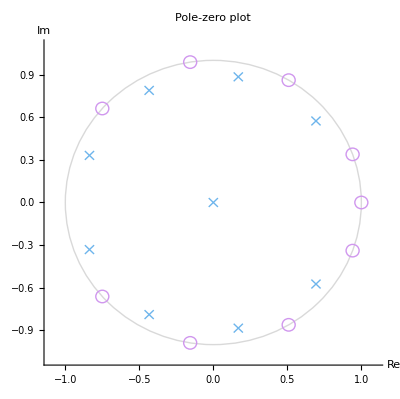

```mathematica
PoleZeroPlot[H[z],z,
AxesLabel->{"Re","Im"},
Prolog->{LightGray,Circle[]},
MarkerScale->Scaled[0.02],PlotLabel->"Pole-zero plot \n"
]
```

```mathematica
Plot[Abs[H[ⅇ^(ⅉ ω)]], {ω, -Pi, Pi},
PlotRange->{{-Pi,Pi},{0,0.43}}, 
AxesLabel->{"ω","|H(ⅇ^ⅉω)|"},
PlotLabel->"Frequency response \n" ,ColorFunction->Function[{x,y},ColorData["Pastel"][y]], 
PlotStyle->Medium
]
```

-Graphics-

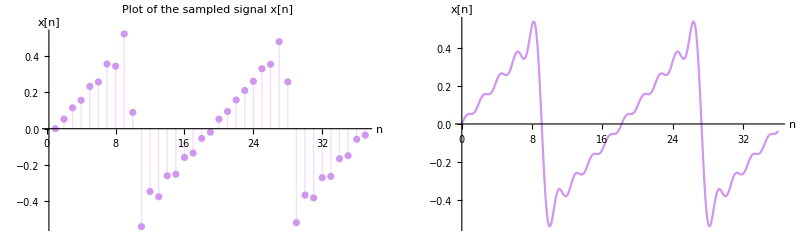

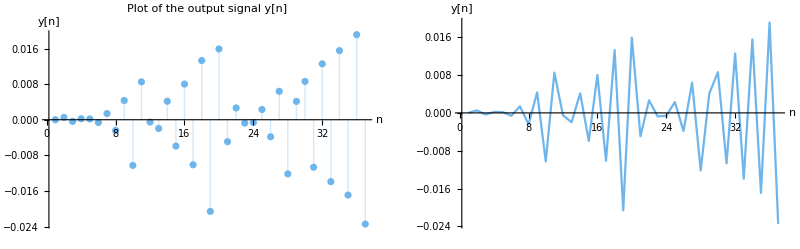

```mathematica
f0=220;T0=1/f0;fs=1/T;T=1/4000;omega=2π f0;omegaHat=omega/fs;
x[n_]=1/π∑_(k=1)^9 (-1 )^(k-1)/k Sin[omegaHat k n];
xn=Table[x[n],{n,0,36}];
xn listplot=ListPlot[xn,
PlotRange->All,
PlotStyle->ColorData["Pastel"][0.1] ,
Filling->Axis,
PlotLabel->
StringForm["`1`[`2`]",Style["x",Italic],Style["n",Italic]]
"Plot of the sampled signal",
AxesLabel->{
Style["n",Italic],
StringForm["`1`[`2`]",Style["x",Italic],Style["n",Italic]]
}
];
xn lineplot=Plot[x[n],{n,0,36},
PlotRange->All,
PlotStyle->ColorData["Pastel"][0.1] ,
AxesLabel->{
Style["n",Italic],
StringForm["`1`[`2`]",Style["x",Italic],Style["n",Italic]]
}
];
yn=OutputResponse[Hz tfm,xn];
yn listplot=ListPlot[yn, 
PlotRange->All,
PlotStyle->ColorData["Pastel"][1] ,
Filling->Axis,
PlotLabel->
StringForm["`1`[`2`]",Style["y",Italic],Style["n",Italic]]
"Plot of the output signal",
AxesLabel->{
Style["n",Italic],
StringForm["`1`[`2`]",Style["y",Italic],Style["n",Italic]]
}
];
yn lineplot=ListLinePlot[yn, 
PlotRange->All,
PlotStyle->ColorData["Pastel"][1] ,
AxesLabel->{
Style["n",Italic],
StringForm["`1`[`2`]",Style["y",Italic],Style["n",Italic]]
}
];
GraphicsRow[{xn listplot,xn lineplot}]
GraphicsRow[{yn listplot,yn lineplot}]
```

```mathematica
xnF=Fourier[xn]; ynF = Fourier[yn];
FourierShift[a_List]:=Module[{d=Dimensions[a]},RotateRight[a,Quotient[d,2]]];
InverseFourierShift[a_List]:=Module[{d=Dimensions[a]},RotateLeft[a,Quotient[d,2]]];
xnFs = FourierShift[xnF]; ynFs = FourierShift[ynF];
```

```mathematica
xn freq listplot=ListPlot[Abs[xnFs],
DataRange->{-18,18},
PlotRange->All,
PlotStyle->ColorData["Pastel"][0.1] ,
Filling->Axis,
PlotLabel->"Spectrum of the sampled signal"
];
xn freq lineplot=ListLinePlot[Abs[xnFs],
DataRange->{-18,18},
PlotRange->All,
PlotStyle->ColorData["Pastel"][0.1] 
];
yn freq listplot=ListPlot[Abs[ynFs], 
DataRange->{-18,18},
PlotRange->All,
PlotStyle->ColorData["Pastel"][1] ,
Filling->Axis,
PlotLabel->"Spectrum of the output signal"
];
yn freq lineplot=ListLinePlot[Abs[ynFs], 
DataRange->{-18,18},
PlotRange->All,
PlotStyle->ColorData["Pastel"][1] 
];
GraphicsRow[{xn freq listplot,xn freq lineplot}]
GraphicsRow[{yn freq listplot,yn freq lineplot}]
```

-Graphics-

-Graphics-

### Part 2

```mathematica
ClearAll["`*"]
```

```mathematica
x[t_]=(ⅇ^(-50 t) Cos[2 π 100 t]+ⅇ^(-75 t) Cos[2 π 200 t]+ⅇ^(-100 t) Cos[2 π 300 t])UnitStep[t];
```

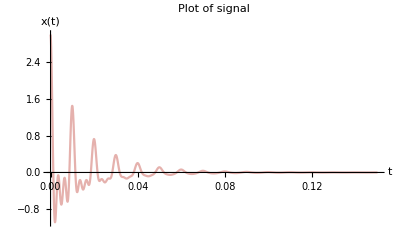

```mathematica
Plot[x[t], {t, 0 , 0.15}, PlotRange->All,PlotLabel->"Plot of signal", AxesLabel->{Style["t",Italic],
StringForm["`1`(`2`)",Style["x",Italic],Style["t",Italic]]}, 
ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium
]
```

```mathematica
X[ω_]=FourierTransform[x[t],t, ω]
```

((-50+ⅈ ω)/(-40000 π^2+(50 ⅈ+ω)^2)+(-75+ⅈ ω)/(-160000 π^2+(75 ⅈ+ω)^2)+(-100+ⅈ ω)/(-360000 π^2+(100 ⅈ+ω)^2))/(√(2 π))

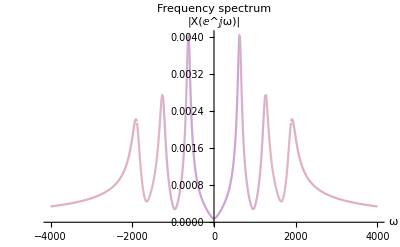

```mathematica
Plot[Abs[X[ω]], {ω, - 4000, 4000},AxesLabel->{"ω","|X(ⅇ^ⅉω)|"},PlotLabel->"Frequency spectrum \n",ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium]
```

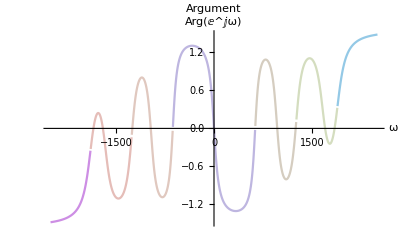

```mathematica
Plot[Arg[X[ω]], {ω, - 2500, 2500},AxesLabel->{"ω","Arg(ⅇ^ⅉω)"},PlotLabel->"Argument \n",ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium]
```

```mathematica
ListLinePlot[Table[N[Abs[X[ω]]], {ω, 1000π}], ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium]
```

-Graphics-

```mathematica
max=FindPeaks[Table[N[Abs[X[ω]]], {ω, 1000π}]]
```

{{627,0.00405668},{1263,0.00276316},{1911,0.00222517}}

```mathematica
(* To get the minimum value we shift the graph around the x axis. We then use the function FindPeaks to find the maximum values. The maximum values will no be under the x axis and the should be over.*)
```

```mathematica
min=FindPeaks[Table[N[-Abs[X[ω]]], {ω, 1000π}]]
```

{{1,-0.0000802974},{958,-0.000282227},{1647,-0.000450278},{3141,-0.000481222}}

```mathematica
ListLinePlot[Table[N[-Abs[X[ω]]], {ω, 1000π}], ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium]
```

-Graphics-

```mathematica
(*To get the right minimum values we change the y values from negative to positive.*)
```

```mathematica
minR=Abs[min]
```

{{1,0.0000802974},{958,0.000282227},{1647,0.000450278},{3141,0.000481222}}

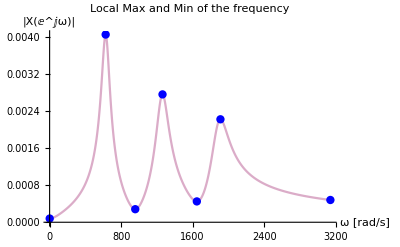

```mathematica
ListLinePlot[Table[N[Abs[X[ω]]], {ω, 1000π}],
Epilog->{Blue,PointSize[0.015],Point[Join[minR, max]]},
PlotLabel->"Local Max and Min of the frequency",AxesLabel->{"ω [rad/s]","|X(ⅇ^ⅉω)|"}, ColorFunction->Function[{x,y},ColorData["Pastel"][y]], PlotStyle->Medium, PlotRange -> Automatic]
```